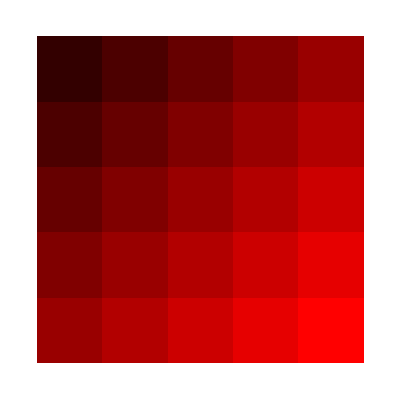

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"];
Needs["gBRDF`"];
Needs["gUtils`"];
SetDirectory[NotebookDirectory[]];

f=Table[1,5,5];
For[i=1,i≤5,i++,
For[j=1,j≤5,j++,
 f[[i]][[j]]=RGBColor[(i+j)*0.1,0,0];
]
];
ArrayPlot[f]


(*testColor[x_,y_,data_]:=Module[];
Show[pltRect2D[<|"min"->{0,0},"max"->{1,1},
   "colorFunc"->Function[{x,y},Blue]|>],
	ImageSize->Medium];*)
```

```mathematica
ArrayPlot[Table[0,{x,4},{y,5}],Mesh->True,PixelConstrained->25]
```

-Graphics-

```mathematica
Range
```